# Switching Strategy for Persister Eradication

```mathematica
A={{Kn,b},{a,Kp}};
MatrixForm[A]
```

(Kn | b
a | Kp)

```mathematica
Eigenvalues[A]
FullSimplify[%]
```

{1/2 (Kn+Kp-√(4 a b+Kn^2-2 Kn Kp+Kp^2)),1/2 (Kn+Kp+√(4 a b+Kn^2-2 Kn Kp+Kp^2))}

{1/2 (Kn-√(4 a b+(Kn-Kp)^2)+Kp),1/2 (Kn+√(4 a b+(Kn-Kp)^2)+Kp)}

```mathematica
Clear[tON,tOFF]
```

```mathematica
(*KnON=-3.5526;
KpON=-0.17095;*)
KnON=-3.8;
KpON=-0.2;
aON=0(*1.5*10^(-15)*);
bON=0.0;
ON={{KnON,bON},{aON,KpON}}
```

{{-3.8,0.},{0,-0.2}}

```mathematica
Eigenvalues[ON]
```

{-3.8,-0.2}

```mathematica
Eigenvectors[ON]
```

{{-1.,0.},{0.,-1.}}

```mathematica
Inverse[Eigenvectors[ON]]
```

{{-1.,0.},{0.,-1.}}

```mathematica
(*KnOFF= 0.6976;
KpOFF= -1.1194;
aOFF=0.0;
bOFF= 1.1194;*)
KnOFF= 1.35;
KpOFF= -1.2;
aOFF=0.0;
bOFF= 1.2;
OFF={{KnOFF,bOFF},{aOFF,KpOFF}}
```

{{1.35,1.2},{0.,-1.2}}

```mathematica
Eigenvalues[OFF]
```

{1.35,-1.2}

```mathematica
Eigenvectors[OFF]
```

{{1.,0.},{-0.425797,0.904819}}

```mathematica
Inverse[Eigenvectors[OFF]]
```

{{1.,0.},{0.470588,1.10519}}

```mathematica
Eigenvectors[OFF].Inverse[Eigenvectors[OFF]]
```

{{1.,0.},{0.,1.}}

```mathematica
M[tON_,tOFF_]:=MatrixExp[OFF*tOFF]*MatrixExp[ON*tON]
```

```mathematica
M[tON,tOFF]//MatrixForm//FullSimplify
```

(1. ⅇ^(1.35 tOFF-3.8 tON) | 0
0. | 1. ⅇ^(-1.2 tOFF-0.2 tON))

```mathematica
eigenVal[tON_,tOFF_]:=Eigenvalues[M[tON,tOFF]]
eigenVec[tON_,tOFF_]:=Eigenvectors[M[tON,tOFF]]
```

```mathematica
Log10[eigenVal[0.4, 1]]
```

{-0.0738301,-0.555897}

```mathematica
eigenVec[1,1.5]
```

{{-1.,0.},{0.,-1.}}

### Check integration of ODEs in growth

```mathematica
nOFF0=10^7.8
f0=9.*10^(-7)
pOFF0=nOFF0*f0
tmax=3;
solOFF=NDSolve[{nOFF'[t]==KnOFF*nOFF[t]+bOFF*pOFF[t],
pOFF'[t]==aOFF*nOFF[t]+bOFF*pOFF[t],
nOFF[0]==nOFF0,pOFF[0]==pOFF0},{nOFF[t],pOFF[t]},{t,0,tmax}]
```

6.30957×10^7

9.×10^-7

56.7862

{{nOFF[t]→InterpolatingFunction[…][t],pOFF[t]→InterpolatingFunction[…][t]}}

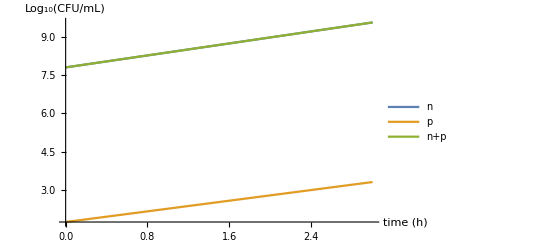

```mathematica
Plot[Evaluate[{Log10[nOFF[t]],Log10[pOFF[t]],Log10[nOFF[t]+pOFF[t]]}/.solOFF],{t,0,tmax},
AxesLabel->{"time (h)","Log_10(CFU/mL)"},
PlotLegends->{n,p,n+p}]
```

```mathematica
Log10[Max[Re[eigenVal[tON,tOFF]]]]/(tON+tOFF)/.{tON->3,tOFF->2}
```

-0.260577

```mathematica
kkk1=Log10[eigenVal[tON,tOFF]][[2]]/(tON+tOFF)/.{tON->3,tOFF->2}
kkk2=Log10[eigenVal[tON,tOFF]][[1]]/(tON+tOFF)/.{tON->3,tOFF->2}
kkksqrt=-Sqrt[kkk1*kkk2]
```

-0.260577

-0.755672

-0.443746

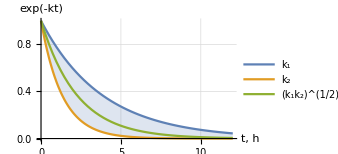

```mathematica
tmax=12;
Plot[Evaluate[
{Exp[kkk1*t],Exp[kkk2*t],Exp[kkksqrt*t]}
],
{t,0,tmax},
ImageSize->250,
BaseStyle->"Medium",
GridLines->Automatic,
Filling->{1->{2}},
AxesLabel->{"t, h","exp(-kt)"},
PlotLegends->{"k_1","k_2","(k_1k_2)^(1/2)"}
]
```

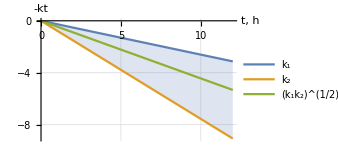

```mathematica
tmax=12;
Plot[Evaluate[
{kkk1*t,kkk2*t,kkksqrt*t}
],
{t,0,tmax},
ImageSize->250,
BaseStyle->"Medium",
GridLines->Automatic,
Filling->{1->{2}},
AxesLabel->{"t, h","-kt"},
PlotLegends->{"k_1","k_2","(k_1k_2)^(1/2)"}
]
```

### Max eigenvalue approximation

```mathematica
-KnON/KnOFF
```

2.81481

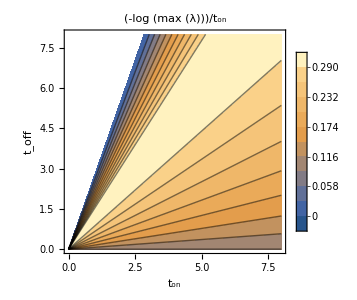

```mathematica
tONmin=0.0;
tONmax=8;
tOFFmin=0.0;
tOFFmax=8;
ContourPlot[
-Log10[Max[Re[eigenVal[tON,tOFF]]]]/(tON+tOFF),
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
PlotPoints->50,
Contours->30,
ContourLabels->Automatic,
PlotLabel->"(-log (max (λ)))/t_on",
FrameLabel->{"t_on","t_off"},
PlotLegends->Automatic,
ImageSize->200
]
```

```mathematica
tONmin=0.;
tONmax=4;
tOFFmin=0.;
tOFFmax=6;
tempLambda1a=Plot3D[
Evaluate[
-Log(*10*)[Max[eigenVal[tON,tOFF]]]/(tON+tOFF)],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
BoxRatios->{1,1,1},
PlotRange->All,
PlotPoints->200,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FaceGrids->{{1,0,0},{0,1,0},{0,0,-1}},
PlotStyle->Opacity[0.8],
AxesLabel->{"t_on, h","t_off, h"},
PlotLabel->"(-ln (SubscriptBox[λ, max]))/t_on, 1/h",
ImagePadding->20,
Mesh->15,
MeshFunctions->{#3&}]
```

-Graphics3D-

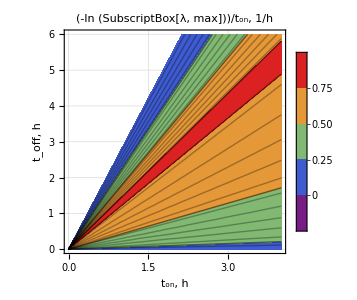

```mathematica
tempLambda1a=ContourPlot[
Evaluate[
-Log(*10*)[Max[eigenVal[tON,tOFF]]]/(tON+tOFF)],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
BoxRatios->{1,1,1},
PlotRange->All,
PlotPoints->30,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
GridLines->Automatic,
AxesLabel->{"t_on, h","t_off, h"},
PlotLabel->"(-ln (SubscriptBox[λ, max]))/t_on, 1/h",
ImagePadding->20,
Mesh->15,
MeshFunctions->{#3&}]
```

-Graphics3D-

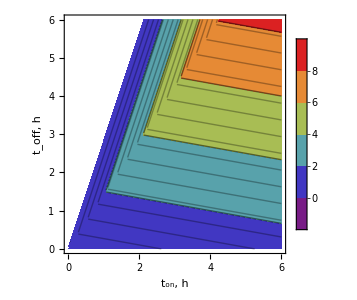

```mathematica
tONmin=0.;
tONmax=6;
tOFFmin=0.;
tOFFmax=6;
tempLambda1a=Plot3D[
Evaluate[
-Log(*10*)[Max[eigenVal[tON,tOFF]]]],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
BoxRatios->{1,1,1},
PlotRange->All,
PlotStyle->Opacity[0.8],
ColorFunction->"Rainbow",
FaceGrids->{{1,0,0},{0,1,0},{0,0,-1}},
AxesLabel->{"t_on, h","t_off, h","-ln(λ_max)"},
PlotPoints->200,
Mesh->15,
MeshFunctions->{#3&}]


tempLambda1a=ContourPlot[
Evaluate[
-Log(*10*)[Max[eigenVal[tON,tOFF]]]],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
BoxRatios->{1,1,1},
PlotRange->All,
(*PlotStyle->Opacity[0.7],*)
ColorFunction->"Rainbow",
AxesLabel->{"t_on, h","t_off, h","-ln(λ_max)"},
PlotPoints->30,
Mesh->15,
MeshFunctions->{#3&},
PlotLegends->Automatic]
```

#### Test approximate linear formula

```mathematica
Log[10.]
```

2.30259

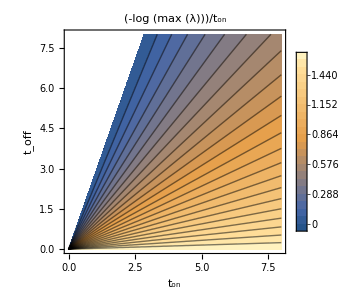

```mathematica
tONmin=0.;
tONmax=8;
tOFFmin=0.;
tOFFmax=8;
ContourPlot[
-(tOFF*KnOFF+tON*KnON)/Log[10.]/(tON+tOFF),
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
PlotPoints->20,
Contours->30,
ContourLabels->Automatic,
PlotLabel->"(-log (max (λ)))/t_on",
FrameLabel->{"t_on","t_off"},
PlotLegends->Automatic,
ImageSize->200
]
```

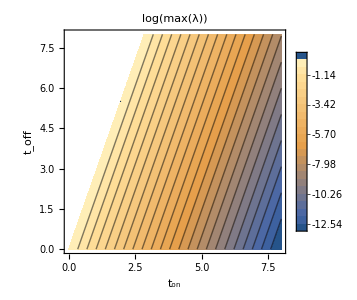

```mathematica
tONmin=0.;
tONmax=8;
tOFFmin=0.;
tOFFmax=8;
ContourPlot[
(tOFF*KnOFF+tON*KnON)/Log[10.],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
PlotPoints->20,
Contours->30,
ContourLabels->Automatic,
PlotLabel->"log(max(λ))",
FrameLabel->{"t_on","t_off"},
PlotLegends->Automatic,
ImageSize->200
]
```

```mathematica
tONmin=0.;
tONmax=4;
tOFFmin=0.;
tOFFmax=6;
Clear[tON,tOFF]
tempLambda1b=Plot3D[
Evaluate[
(tOFF*KnOFF+tON*KnON)/Log[10.]
],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->400,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
BoxRatios->{1,1,1},
PlotRange->All,
PlotStyle->{{Opacity[0.5],Blue}},
AxesLabel->{"t_on","t_off","log_10(λ_1)"},
PlotPoints->20,
Mesh->30,
MeshFunctions->{#3&},
PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
tONmin=0.;
tONmax=4;
tOFFmin=0.;
tOFFmax=6;
tempLambda1a=Plot3D[
Evaluate[
Log10[Max[eigenVal[tON,tOFF]]]],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->400,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
BoxRatios->{1,1,1},
PlotRange->All,
PlotStyle->Opacity[0.7],
AxesLabel->{"t_on","t_off","log_10(max(λ))"},
PlotPoints->20,
Mesh->30,
MeshFunctions->{#3&},
PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
tempLambda1aMesh=Plot3D[
Evaluate[
-Log10[Max[eigenVal[tON,tOFF]]]/(tON+tOFF)],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->400,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
BoxRatios->{1,1,1},
PlotRange->All,
PlotStyle->Opacity[0.7],
AxesLabel->{"t_on","t_off","(-log (max (λ)))/t_on"},
PlotPoints->30,
Mesh->10,
(*MeshFunctions->{#3&},*)
PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
tON=2;
tOFF=3.0;
Log10[eigenVal[tON,tOFF]]
Clear[tON,tOFF]
```

{-1.54175,-1.73718}

### sqrt(lambda1*lambda2) approximation

```mathematica
tONmin=0;
tONmax=10;
tOFFmin=0;
tOFFmax=10;
temp1=ContourPlot[
Evaluate[
Sqrt[
Log(*10*)[Re[
eigenVal[tON,tOFF][[1]]
]]*
Log(*10*)[Re[
eigenVal[tON,tOFF][[2]]
]]
]
/(tON+tOFF)
],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
PlotPoints->50,
GridLines->Automatic,
Contours->14,
ContourLabels->Automatic,
ColorFunction->"Rainbow",
PlotLabel->"[ln (SubscriptBox[λ, 1]) ln (SubscriptBox[λ, 2])]^(1/2)/t_on",
FrameLabel->{"t_on","t_off"},
PlotLegends->Automatic,
ImageSize->200
];
temp11=Plot[
(2 KnON KpON-KnON KpOFF-KnOFF KpON)/(2 KnOFF KpOFF-KnON KpOFF-KnOFF KpON)tON,{tON,tONmin,tONmax},
PlotStyle->White];
Show[temp1,temp11]
```

-Graphics-

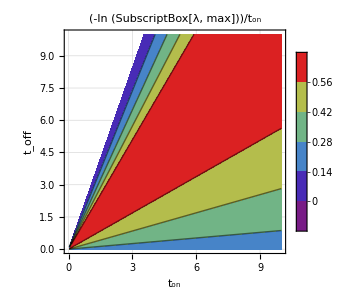

```mathematica
tONmin=0;
tONmax=10;
tOFFmin=0;
tOFFmax=10;
temp1b=ContourPlot[
-Evaluate[
Max[
Log(*10*)[Abs[
eigenVal[tON,tOFF][[1]]
]],
Log(*10*)[Abs[
eigenVal[tON,tOFF][[2]]
]]
]
/(tON+tOFF)
],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
PlotPoints->50,
GridLines->Automatic,
Contours->14,
ContourLabels->Automatic,
ColorFunction->"Rainbow",
PlotLabel->"(-ln (SubscriptBox[λ, max]))/t_on",
FrameLabel->{"t_on","t_off"},
PlotLegends->Automatic,
ImageSize->200
]
(*temp11b=Plot[
(2 KnON KpON-KnON KpOFF-KnOFF KpON)/(2 KnOFF KpOFF-KnON KpOFF-KnOFF KpON)tON,{tON,tONmin,tONmax},
PlotStyle->White];
Show[temp1b,temp11b]*)
```

```mathematica
(*temp1threeD=SliceContourPlot3D[
Evaluate[
Sqrt[
Log(*10*)[Re[
eigenVal[tON,tOFF][[1]]
]]*
Log(*10*)[Re[
eigenVal[tON,tOFF][[2]]
]]
]
/(tON+tOFF)
],
z==0,
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},{z,0,1},
ImageSize->300,
BaseStyle->"Medium",
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
(*ColorFunction->"Rainbow",*)
PlotPoints->50,
(*GridLines->Automatic,*)
Contours->14,
(*ContourLabels->Automatic,*)
PlotLabel->"[ln(SubscriptBox[λ, 1])ln(SubscriptBox[λ, 2])]^(1/2)/t_on",
(*FrameLabel->{"t_on","t_off"},*)
(*PlotLegends->Automatic,*)
ImageSize->200
]*)
```

```mathematica
tONmin=0;
tONmax=6;
tOFFmin=0;
tOFFmax=6;
temp2=Plot3D[
Evaluate[
Sqrt[
Log(*10*)[Abs[
eigenVal[tON,tOFF][[1]]
]]*
Log(*10*)[Abs[
eigenVal[tON,tOFF][[2]]
]]
]
/(tON+tOFF)
],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->400,
BaseStyle->"Medium",
BoxRatios->{1,1,1},
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<-0.1],
PlotRange->All,
PlotStyle->Opacity[0.8],
(*ColorFunction->ColorData["Rainbow"],*)
AxesLabel->{"t_on, h","t_off, h"(*[ln(Subscript[λ, 1])ln(Subscript[λ, 2])]^(1/2)/(Subscript[t, on]+Subscript[t, off])*)},PlotLabel->"k, 1/h",
ColorFunction->"Rainbow",
PlotPoints->150,
FaceGrids->{{1,0,0},{0,1,0},{0,0,-1}},
MaxRecursion->2,
PlotLegends->Automatic,
Mesh->15,
(*MeshStyle->Yellow,*)
MeshFunctions->{#3&}(*,
PlotLegends->Automatic*)]
```

-Graphics3D-

```mathematica
tempLine=ListLinePlot3D[
Evaluate[
{
{
0,
0,
(Sqrt[
Log(*10*)[Abs[
eigenVal[tON,tOFF][[1]]
]]*
Log(*10*)[Abs[
eigenVal[tON,tOFF][[2]]
]]
]
/(tON+tOFF)
)/.{tON->tONmax,tOFF->tONmax*(2 KnON KpON-KnON KpOFF-KnOFF KpON)/(2 KnOFF KpOFF-KnON KpOFF-KnOFF KpON)}
},
{
tONmax,
tONmax*(2 KnON KpON-KnON KpOFF-KnOFF KpON)/(2 KnOFF KpOFF-KnON KpOFF-KnOFF KpON),
(Sqrt[
Log(*10*)[Abs[
eigenVal[tON,tOFF][[1]]
]]*
Log(*10*)[Abs[
eigenVal[tON,tOFF][[2]]
]]
]
/(tON+tOFF)
)/.{tON->tONmax,tOFF->tONmax*(2 KnON KpON-KnON KpOFF-KnOFF KpON)/(2 KnOFF KpOFF-KnON KpOFF-KnOFF KpON)}
}
}
],
Filling->Bottom,
FillingStyle->Directive[Gray,Opacity[0.34]],
PlotStyle->White
];
Show[temp2,tempLine,ImageSize->300,
ImagePadding->20]
```

-Graphics3D-

```mathematica
tONmin=0;
tONmax=4;
tOFFmin=0;
tOFFmax=4;
Plot3D[
-Evaluate[
Max[
Log(*10*)[Abs[
eigenVal[tON,tOFF][[1]]
]],
Log(*10*)[Abs[
eigenVal[tON,tOFF][[2]]
]]
]
/(tON+tOFF)
],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
BoxRatios->{1,1,1},
RegionFunction->Function[{tON,tOFF},tOFF*KnOFF+tON*KnON<=0],
PlotRange->All,
PlotStyle->Opacity[0.8],
(*ColorFunction->ColorData["Rainbow"],*)
FaceGrids->{{1,0,0},{0,1,0},{0,0,-1}},
AxesLabel->{"t_on (h)","t_off (h)","(-ln (SubscriptBox[λ, max]))/t_on"},
ColorFunction->"Rainbow",
PlotPoints->100,
Mesh->22,
MeshFunctions->{#3&}(*,
PlotLegends->Automatic*)]
```

-Graphics3D-

### Maximize decline rate k

```mathematica
k[x_]:=(Knoff*x+Knon)(Kpoff*x+Kpon)/(1+x)^2
```

```mathematica
dkdx[x_]:=D[k[x],x]
Simplify[%]
```

```mathematica
Solve[dkdx[x]==0,x]
Simplify[%]
```

{{x→(-Knon Kpoff-Knoff Kpon+2 Knon Kpon)/(2 Knoff Kpoff-Knon Kpoff-Knoff Kpon)}}

{{x→-(Knon Kpoff+Knoff Kpon-2 Knon Kpon)/(2 Knoff Kpoff-Knon Kpoff-Knoff Kpon)}}

```mathematica
(2 KnON KpON-KnON KpOFF-KnOFF KpON)/(2 KnOFF KpOFF-KnON KpOFF-KnOFF KpON)
```

0.367862

### Other

```mathematica
tONmin=0;
tONmax=8;
tOFFmin=0;
tOFFmax=8;
Plot3D[
{-Log(*10*)[
Re[
eigenVal[tON,tOFF][[1]]
]
]/(tON+tOFF),
-Log(*10*)[
Re[
eigenVal[tON,tOFF][[2]]
]
]/(tON+tOFF)},
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
BoxRatios->{1,1,1},
PlotRange->All,
PlotStyle->Opacity[0.7],
AxesLabel->{"t_on","t_off","(-log (Re (λ)))/t_on"},
PlotPoints->20,
Mesh->30,
MeshFunctions->{#3&}(*,
PlotLegends->Automatic*)]
```

-Graphics3D-

```mathematica
tONmin=0;
tONmax=8;
tOFFmin=0;
tOFFmax=8;
temp10=Plot3D[
{
Log(*10*)[eigenVal[tON,tOFF][[1]]],
Log(*10*)[eigenVal[tON,tOFF][[2]]](*,
0*)
},
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->300,
BaseStyle->"Medium",
BoxRatios->{1,1,1},
PlotRange->{All,All,{-40,20}},
PlotStyle->Opacity[0.7],
(*FaceGrids->{{0,-1,0},{-1,0,0}},*)
AxesLabel->{"t_on, h","t_off, h"},
PlotLabel->"ln(λ_1), ln(λ_2)",
ViewPoint->{3,4,1},
Lighting->Automatic,
PlotPoints->50,
Mesh->30,
MeshFunctions->{#3&},
PlotLegends->{"ln(λ_1)","ln(λ_2)","0"}];
temp20=Plot3D[
0,
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
PlotStyle->{Green, Opacity[0.4]},
Mesh->None];
Show[temp10,temp20];
```

```mathematica
temp30=ContourPlot3D[
Evaluate[
{
Log(*10*)[eigenVal[tON,tOFF][[1]]]==0,
Log(*10*)[eigenVal[tON,tOFF][[2]]]==0
}
],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},{z,-0.2,0.2},
MeshFunctions->{#3&},
MeshStyle->Opacity[0],
MeshShading->{Black}
];
Show[temp10,temp20,temp30]
```

-Graphics3D-

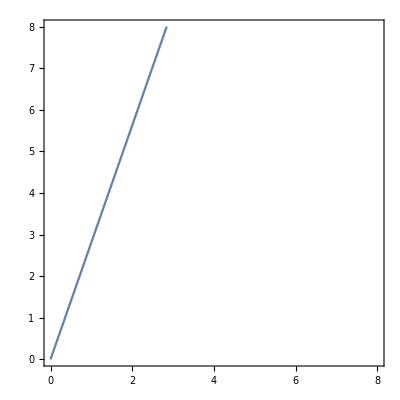

```mathematica
temp30=ContourPlot[
Evaluate[
{
Log(*10*)[eigenVal[tON,tOFF][[1]]]==0,
Log(*10*)[eigenVal[tON,tOFF][[2]]]==0
}
],
{tON,tONmin,tONmax},{tOFF,tOFFmin,tOFFmax},
ImageSize->Tiny
]
```

```mathematica
eigenVal[1,2]
```

{0.332871,0.0742736}

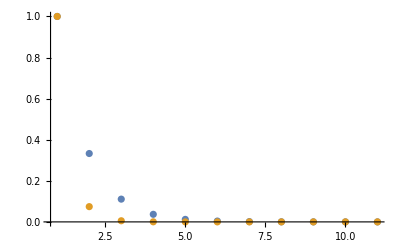

```mathematica
nmax=10;
ListPlot[{Table[eigenVal[1,2][[1]]^n,{n,0,nmax}],
Table[eigenVal[1,2][[2]]^n,{n,0,nmax}]},
ImageSize->"Small",
PlotRange->All]
```

```mathematica
modal=Transpose[eigenVec[2,3]]
```

{{-1.,0.},{0.,-1.}}

```mathematica
Inverse[modal].M[1,2].modal
```

{{0.332871,0.},{0.,0.0742736}}

```mathematica
Inverse[modal];
MatrixForm[%]
```

(-1. | 0.
0. | -1.)

```mathematica
eigen[4,0.5]
```

eigen[4,0.5]

### Optimal ratio t_off/t_on

```mathematica
(2 Subscript[R, n] Subscript[R, p]-Subscript[R, n]-Subscript[R, p])/(2-Subscript[R, n]-Subscript[R, p])
```

(-R_n-R_p+2 R_n R_p)/(2-R_n-R_p)

```mathematica
RnOptimum
RpOptimum
```

RnOptimum

RpOptimum

```mathematica
RnOptimum=KnON/KnOFF
RpOptimum=KpON/KpOFF
Rnmin=0.75RnOptimum;
Rnmax=1.25RnOptimum;
Rpmin=0.75RpOptimum;
Rpmax=1.25RpOptimum;
tempOpt1=Plot3D[Evaluate[{(2Rp*Rn-Rp-Rn)/(2-Rn-Rp)/.{Rn->RnOptimum,Rp->RpOptimum},(2Rp*Rn-Rp-Rn)/(2-Rn-Rp)}
],
{Rn,Rnmin,Rnmax},{Rp,Rpmin,Rpmax},
PlotRange->All,
BoxRatios->{1, 1, 1},
BaseStyle->"Medium",
PlotStyle->Opacity[0.7],
ColorFunction->{"Rainbow"},
FaceGrids->{(*{1,0,0},{0,1,0},*){{0,0,-1},{{RnOptimum},{RpOptimum}}}},
MeshFunctions->{#3&},
AxesLabel->{Subscript[R, n],Subscript[R, p],"(t_off/t_on)_opt"},
PlotLegends->Automatic
];
tempOpt2=ListPointPlot3D[
{
{Rn,Rp,(2Rp*Rn-Rn-Rp)/(2-Rp-Rn)},
{Rn,Rp,(2Rp*Rn-Rn-Rp)/(2-Rp-Rn)}
}
/.{Rn->RnOptimum,Rp->RpOptimum},

PlotRange->{{Rpmin,Rpmax},{Rnmin,Rnmax}},
BoxRatios->{1, 1, 1},
PlotStyle->Black,
FaceGrids->{(*{1,0,0},{0,1,0},*){{0,0,-1},{{RnOptimum},{RpOptimum}}}},
AxesLabel->{Subscript[R, n],Subscript[R, p],"(t_off/t_on)_opt"},
Filling->Bottom,
FillingStyle->{Black}
];
tempOpt3=Plot3D[Evaluate[{(-Rn)/(2-Rn)}
],
{Rn,Rnmin,Rnmax},{Rp,Rpmin,Rpmax},
PlotRange->All,
BoxRatios->{1, 1, 1},
BaseStyle->"Medium",
PlotStyle->Opacity[0.7],
ColorFunction->{"Rainbow"},
FaceGrids->{(*{1,0,0},{0,1,0},*){{0,0,-1},{{RnOptimum},{RpOptimum}}}},
MeshFunctions->{#3&},
AxesLabel->{Subscript[R, n],Subscript[R, p],"(t_off/t_on)_opt"},
PlotLegends->Automatic
];
Show[tempOpt1,tempOpt2]
(*Show[tempOpt3,tempOpt2]*)
(*Show[tempOpt2,tempOpt1]
*)
```

-2.81481

0.166667

-Graphics3D-